Finite element models of elasto-plastic materials
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 13 December 2021 - Contact: m.marino@ing.uniroma2.it

# Elements

## Q1EPS - Elasto-plasticity (small strain)

#### Initialization

```mathematica
<<AceGen`;

SMSInitialize["Q1EPS","Environment"-> "AceFEM","Mode"-> "Optimal"];

SMSTemplate["SMSTopology"->"Q1",
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson", "σYO -yield", "H -Hardening"},
 "SMSDefaultData" -> {100,0.49,1,10},

(*Time history element data*)
"SMSNoTimeStorage"-> lhg es$$["id","NoIntPoints"],
"SMSPostIterationCall"->True,

(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(*Number of element hystory variables*)
nhg =5; 
lhg=nhg+1;
)
```

#### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,σYO,H}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];

(*ISOPARAMETRIC MAPPING*)
𝕏⊢SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];

ϵ=SMSVariables[𝔻];
GaussPointComputation[Ig];
Ψe⊨ElastoPlastic["EN",𝕙g];
)

ElastoPlastic[task_,𝕙g_]:=(
(*History variables*)
𝔻p={{𝕙g⟦1⟧,𝕙g⟦3⟧},{𝕙g⟦3⟧,𝕙g⟦2⟧}};
α⊢SMSFreeze[𝕙g⟦4⟧];
λ=𝕙g⟦5⟧;

(*Pseudo-energy*)
SMSFreeze[𝔻e,𝔻-𝔻p,"Symmetric"->True];
{λe,μe}⊢SMSHookeToLame[Ee,ν];
Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α^2;
If[task=="EN", Return[Ψe]];

(*Static quantities*)
SMSFreeze[σ,SMSD[Ψe,𝔻e,
		"Symmetric"->True],
			"Symmetric"->True];
SMSFreeze[q,-SMSD[Ψe,α]];

(*Yield function*)
σdev=σ-1/3 IdentityMatrix[ndim]Tr[σ];
fg⊨SMSSqrt[3/2 Tr[σdev.σdev]]-(σYO-q);
If[task=="f", Return[fg]];

(*Flow rule*)
𝕟σ=SMSD[fg,σ,"Symmetric"->True];
𝕟q=SMSD[fg,q];
𝔻pn={{𝕙gnIO⟦1⟧,𝕙gnIO⟦3⟧},
{𝕙gnIO⟦3⟧,𝕙gnIO⟦2⟧}};
αn=𝕙gnIO⟦4⟧;
λn=𝕙gnIO⟦5⟧;
ℚϵ=𝔻p-𝔻pn-(λ-λn)𝕟σ;
Qq=α-αn-(λ-λn)𝕟q;
Qλ=fg;
ℚ={ℚϵ⟦1,1⟧,ℚϵ⟦2,2⟧,ℚϵ⟦1,2⟧,Qq,Qλ};
If[task=="Q", Return[ℚ]];
)

GaussPointComputation[Ig_]:=(
Ihg⊢SMSInteger[(Ig-1)lhg];
(*Algorithm parameters*)
tol⊢SMSReal[rdata$$["SubIterationTolerance"]];
iNR⊢SMSInteger[idata$$["Iteration"]];
(*Previous time step*)
𝕙gnIO⊢SMSIO["Element time dependent data n"[Table[Ihg+i,{i,nhg}]]];
staten⊢SMSIO["Element time dependent data n"[Ihg+nhg+1]];
(*Initialize trial: plastic variables are freezed*)
ftr⊨ElastoPlastic["f",𝕙gnIO];

SMSIf[(iNR==1 && staten==0)||(iNR>1 && ftr<tol)];
	(*Elastic step*)
	𝕙g⫤𝕙gnIO;
	SMSIO[Join[𝕙g,{0}],"Export to",
			"Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
SMSElse[];
	(*Plastic step*)
	𝕙gb⫤𝕙gnIO;
	SMSDo[jNR,1,30,1,𝕙gb];
		ℚg⊨ElastoPlastic["Q",𝕙gb];
		𝔸g⊨SMSD[ℚg,𝕙gb];
		Δ𝕙⊨SMSLinearSolve[𝔸g,-ℚg];
		𝕙gb⊣𝕙gb+Δ𝕙;
		
		SMSIf[SMSSqrt[Δ𝕙.Δ𝕙]<tol];
			SMSIO[Join[𝕙gb,{1}], "Export to", 
				  "Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
			D𝕙Dϵ⫤SMSLinearSolve[𝔸g,-SMSD[ℚg,ϵ,"Constant"->𝕙gb]];
			SMSBreak[];
		SMSEndIf[D𝕙Dϵ];
		
		SMSIf[jNR=="29"];
		SMSExport[{1,2},{idata$$["SubDivergence"],idata$$["ErrorStatus"]}];
			SMSBreak[];
		SMSEndIf[];
	SMSEndDo[𝕙gb,D𝕙Dϵ];

	𝕙g⊣SMSFreeze[𝕙gb,"Dependency"->{ϵ,D𝕙Dϵ}];
SMSEndIf[𝕙g];
)
```

#### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i,"Constant"->𝕙g];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

#### Post - processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
𝔻p⊨𝔻-𝔻e;
σ⊨SMSD[Ψe,𝔻e,"Symmetric"->True];
σdev⊨σ-1/3 IdentityMatrix[ndim]Tr[σ];
σVM⊨SMSSqrt[3/2 Tr[σdev.σdev]];

SMSIO[
{"ϵxx"->𝔻⟦1,1⟧,"ϵxy"->𝔻⟦1,2⟧,"ϵyy"->𝔻⟦2,2⟧,"ϵexx"->𝔻e⟦1,1⟧,"ϵexy"->𝔻e⟦1,2⟧,"ϵeyy"->𝔻e⟦2,2⟧,"ϵpxx"->𝔻p⟦1,1⟧,"ϵpxy"->𝔻p⟦1,2⟧,"ϵpyy"->𝔻p⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"σVM"-> σVM,"α"->α,"λ"->λ,"Ψe"->Ψe}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
```

#### Code generation

```mathematica
SMSWrite[];
{{"File: ""Q1EPS.c""  Size: "20949"  Time: "8}, {{{"Method", "SKR", "SPP"}, {"No.Formulae", 246, 185}, {"No.Leafs", 3340, 2548}}}}
```

## Q1EPS-2

### Initialization

```mathematica
<<AceGen`;

SMSInitialize["Q1EPS2","Environment"-> "AceFEM","Mode"-> "Optimal"];

SMSTemplate["SMSTopology"->"Q1",
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson", "σYO -yield", "H -Hardening"},
 "SMSDefaultData" -> {100,0.49,1,10},

(*Time history element data*)
"SMSNoTimeStorage"-> lhg es$$["id","NoIntPoints"],
"SMSPostIterationCall"->True,

(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(*Number of element hystory variables*)
nhg =7; 
lhg=nhg+1;
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,σYO,H}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];

(*ISOPARAMETRIC MAPPING*)
𝕏⊢SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];

ϵ=SMSVariables[𝔻];
GaussPointComputation[Ig];
Ψe⊨ElastoPlastic["EN",𝕙g];
)

ElastoPlastic[task_,𝕙g_]:=(
(*History variables*)
𝔻p={{𝕙g⟦1⟧,𝕙g⟦3⟧},{𝕙g⟦3⟧,𝕙g⟦2⟧}};
(*α⊢SMSFreeze[𝕙g⟦4⟧];*)
SMSFreeze[α,{{𝕙g⟦4⟧,𝕙g⟦6⟧},{𝕙g⟦6⟧,𝕙g⟦5⟧}},"Symmetric"->True];
(*λ=𝕙g⟦5⟧;*)
λ=𝕙g⟦7⟧;

(*Pseudo-energy*)
SMSFreeze[𝔻e,𝔻-𝔻p,"Symmetric"->True];
{λe,μe}⊢SMSHookeToLame[Ee,ν];
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α^2;*)
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 Transpose[α]H α;*)
Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H Tr[Transpose[α].α];
If[task=="EN", Return[Ψe]];

(*Static quantities*)
SMSFreeze[σ,SMSD[Ψe,𝔻e,
		"Symmetric"->True],
			"Symmetric"->True];
SMSFreeze[q,-SMSD[Ψe,α,"Symmetric"->True],"Symmetric"->True];

(*Yield function*)
σdev=σ-1/3 IdentityMatrix[ndim] Tr[σ];
(*fg⊨SMSSqrt[3/2 Tr[σdev.σdev]]-(σYO-q);*)
(*fg⊨SMSSqrt[3/2 Norm[σdev-q]]-(σYO);(* LA RADICE ?????*)*)
fg⊨SMSSqrt[3/2 Tr[Transpose[σdev-q].(σdev-q)]]-(σYO);
If[task=="f", Return[fg]];

(*Flow rule*)
𝕟σ=SMSD[fg,σ,"Symmetric"->True];
𝕟q=SMSD[fg,q,"Symmetric"->True];
𝔻pn={{𝕙gnIO⟦1⟧,𝕙gnIO⟦3⟧},
{𝕙gnIO⟦3⟧,𝕙gnIO⟦2⟧}};
(*αn=𝕙gnIO⟦4⟧;*)
αn={{𝕙gnIO⟦4⟧,𝕙gnIO⟦6⟧},
{𝕙gnIO⟦6⟧,𝕙gnIO⟦5⟧}};
λn=𝕙gnIO⟦7⟧;
ℚϵ=𝔻p-𝔻pn-(λ-λn)𝕟σ;
Qq=α-αn-(λ-λn)𝕟q;
Qλ=fg;
ℚ={ℚϵ⟦1,1⟧,ℚϵ⟦2,2⟧,ℚϵ⟦1,2⟧,Qq⟦1,1⟧,Qq⟦2,2⟧,Qq⟦1,2⟧,Qλ};
If[task=="Q", Return[ℚ]];
)

GaussPointComputation[Ig_]:=(
Ihg⊢SMSInteger[(Ig-1)lhg];
(*Algorithm parameters*)
tol⊢SMSReal[rdata$$["SubIterationTolerance"]];
iNR⊢SMSInteger[idata$$["Iteration"]];
(*Previous time step*)
𝕙gnIO⊢SMSIO["Element time dependent data n"[Table[Ihg+i,{i,nhg}]]];
staten⊢SMSIO["Element time dependent data n"[Ihg+nhg+1]];
(*Initialize trial: plastic variables are freezed*)
ftr⊨ElastoPlastic["f",𝕙gnIO];

SMSIf[(iNR==1 && staten==0)||(iNR>1 && ftr<tol)];
	(*Elastic step*)
	𝕙g⫤𝕙gnIO;
	SMSIO[Join[𝕙g,{0}],"Export to",
			"Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
SMSElse[];
	(*Plastic step*)
	𝕙gb⫤𝕙gnIO;
	SMSDo[jNR,1,30,1,𝕙gb];
		ℚg⊨ElastoPlastic["Q",𝕙gb];
		𝔸g⊨SMSD[ℚg,𝕙gb];
		Δ𝕙⊨SMSLinearSolve[𝔸g,-ℚg];
		𝕙gb⊣𝕙gb+Δ𝕙;
		
		SMSIf[SMSSqrt[Δ𝕙.Δ𝕙]<tol];
			SMSIO[Join[𝕙gb,{1}], "Export to", 
				  "Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
			D𝕙Dϵ⫤SMSLinearSolve[𝔸g,-SMSD[ℚg,ϵ,"Constant"->𝕙gb]];
			SMSBreak[];
		SMSEndIf[D𝕙Dϵ];
		
		SMSIf[jNR=="29"];
		SMSExport[{1,2},{idata$$["SubDivergence"],idata$$["ErrorStatus"]}];
			SMSBreak[];
		SMSEndIf[];
	SMSEndDo[𝕙gb,D𝕙Dϵ];

	𝕙g⊣SMSFreeze[𝕙gb,"Dependency"->{ϵ,D𝕙Dϵ}];
SMSEndIf[𝕙g];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i,"Constant"->𝕙g];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
𝔻p⊨𝔻-𝔻e;
σ⊨SMSD[Ψe,𝔻e,"Symmetric"->True];
σdev⊨σ-1/3 IdentityMatrix[ndim]Tr[σ];
σVM⊨SMSSqrt[3/2 Tr[σdev.σdev]];

SMSIO[
{"ϵxx"->𝔻⟦1,1⟧,"ϵxy"->𝔻⟦1,2⟧,"ϵyy"->𝔻⟦2,2⟧,"ϵexx"->𝔻e⟦1,1⟧,"ϵexy"->𝔻e⟦1,2⟧,"ϵeyy"->𝔻e⟦2,2⟧,"ϵpxx"->𝔻p⟦1,1⟧,"ϵpxy"->𝔻p⟦1,2⟧,"ϵpyy"->𝔻p⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"σVM"-> σVM,"α"->α,"λ"->λ,"Ψe"->Ψe}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
```

### Code generation

```mathematica
SMSWrite[];
```

File: Q1EPS2.c  Size: 29542  Time: 16
Method | SKR | SPP
No.Formulae | 338 | 268
No.Leafs | 5250 | 4108

# FEM Simulations

## Patch test

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
myPatch[element_,OptionsPattern[]]:=(
L=1;
ϵmax=0.1;

<<AceFEM`;
SMTInputData[];
(*SMTAddDomain["Ωc","Q1EPS",{"E *"-> 100,"ν *"-> 0.3,"σYO *"->5,"H *"->10}];*)
SMTAddDomain["Ωc",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}];


SMTAddNode[L{{0.0,0.0},{0.0,1.0},{0.2,0.15},{0.75,0.3},{1.0,0.0},{0.25,0.7},{0.75,0.75},{1.0,1.0}}];
SMTAddElement[{{"Ωc",{1,5,4,3}},{"Ωc",{1,3,6,2}},{"Ωc",{2,6,7,8}},{"Ωc",{8,7,4,5}},{"Ωc",{7,6,3,4}}}];

SMTAddEssentialBoundary[Point[{0,0},"D"],1->0,2->0];
SMTAddEssentialBoundary[Point[{0,L},"D"],1->0,2->ϵmax L];
SMTAddEssentialBoundary[Point[{L,0},"D"],2->0];
SMTAddEssentialBoundary[Point[{L,L},"D"],2->ϵmax L];
SMTAnalysis[];
)
Options[myPatch]={"σYO"->5,"H"->10}
```

{σYO→5,H→10}

### Solution algorithm (loading-unloading, adaptive)

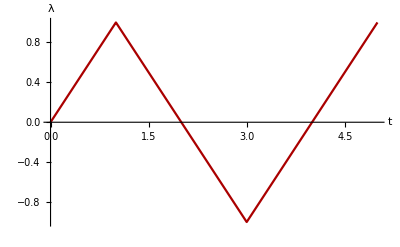

```mathematica
tMax=5;
λf[t_]:=If[OddQ[Floor[(t+1)/2]],1,-1] (2 Floor[(t+1)/2]-t);
Plot[λf[t],{t,0,tMax},AxesLabel->{"t","λ"},
PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

```mathematica
SolveMyPatch[]:=(
tMax=5;
λf[t_]:=If[OddQ[Floor[(t+1)/2]],1,-1] (2 Floor[(t+1)/2]-t);
Clear[σ]; σ={{0,0}};
t0=0.1;ΔtMin=0.0001;ΔtMax=0.1;
tolNR=10^-8;maxNR=50;targetNR=15;
SMTNextStep["t"->t0,"λ[t]"->λf];
While[ 
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive Time",targetNR,ΔtMin,ΔtMax,tMax}]
,SMTNewtonIteration[];];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];]; 
step⟦3⟧ ,If[step⟦1⟧
,SMTStepBack[];,
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
];
SMTNextStep["Δt"->step⟦2⟧,"λ[t]"->λf];];
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
Return[σ];
)
```

### Results

```mathematica
<<AceFEM`
```

σyo=175, H=11600/11

-Graphics-

σyo=200, H=11600/11

-Graphics-

σyo=225, H=11600/11

-Graphics-

σyo=250, H=11600/11

-Graphics-

σyo=275, H=11600/11

-Graphics-

σyo=300, H=11600/11

-Graphics-

σyo=325, H=11600/11

-Graphics-

σyo=350, H=11600/11

-Graphics-

σyo=375, H=11600/11

-Graphics-

σyo=400, H=11600/11

-Graphics-

σyo=425, H=11600/11

-Graphics-

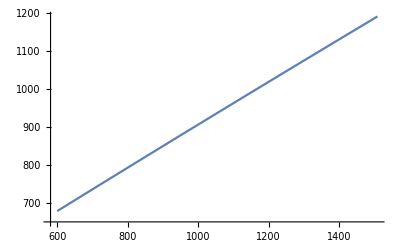

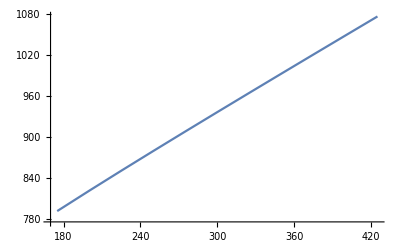

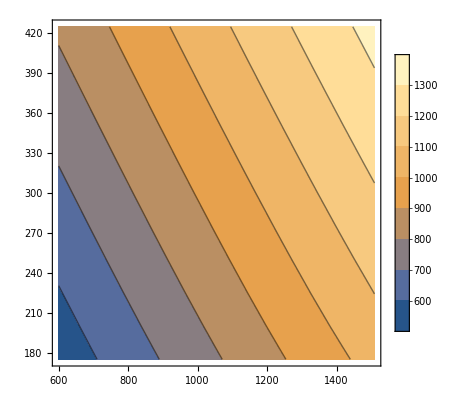

```mathematica
Npassi=11;
harden=Table[600+i((1600-600)/Npassi),{i,0,Npassi-1}];
σyo=Table[175+i((450-175)/Npassi),{i,0,Npassi-1}];
myσ=Table[{0i,0j},{i,1,Length[harden]},{j,1,Length[σyo]}];
Do[Do[
myPatch["Q1EPS","σYO"->σyo⟦j⟧,"H"->harden⟦i⟧];
σ=SolveMyPatch[];
myσ⟦i,j⟧=Max[σ];
If[i==(Length[myσ]+1)/2,
Print["σyo=",σyo⟦j⟧,", H=",harden⟦i⟧];
Print[ListLinePlot[σ,AxesLabel->{"ϵyy","σyy"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]]]
,{i,1,Length[harden]}],{j,1,Length[σyo]}]
ListLinePlot[Table[{harden⟦i⟧,myσ⟦i,(Length[myσ]+1)/2⟧},{i,1,Length[myσ]}]]
ListLinePlot[Table[{σyo⟦i⟧,myσ⟦(Length[myσ]+1)/2,i⟧},{i,1,Length[myσ]}]]
list=Flatten[Table[{harden⟦i⟧,σyo⟦j⟧,myσ⟦i,j⟧},{i,1,Length[myσ]},{j,1,Length[myσ]}],1];
ListContourPlot[list,PlotLegends->Automatic]
```

```mathematica
ListLinePlot[σ,AxesLabel->{"ϵyy","σyy"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

{{0,0},{0.01,404.611},{0.02,419.694},{0.03,434.778},{0.04,449.861},{0.05,464.945},{0.06,480.029},{0.07,495.112},{0.08,510.196},{0.09,525.279},{0.1,540.363},{0.09,-547.167},{0.08,-562.25},{0.07,-577.334},{0.06,-592.418},{0.05,-607.501},{0.04,-622.585},{0.03,-637.668},{0.02,-652.752},{0.01,-667.835},{-4.57786×10^-17,-682.919},{-0.01,-698.002},{-0.02,-713.086},{-0.03,-728.169},{-0.04,-743.253},{-0.05,-758.337},{-0.06,-773.42},{-0.07,-788.504},{-0.08,-803.587},{-0.09,-818.671},{-0.1,-833.754},{-0.09,836.063},{-0.08,851.147},{-0.07,866.23},{-0.06,881.314},{-0.05,896.397},{-0.04,911.481},{-0.03,926.564},{-0.02,941.648},{-0.01,956.731},{1.79815×10^-16,971.815},{0.01,986.899},{0.02,1001.98},{0.03,1017.07},{0.04,1032.15},{0.05,1047.23},{0.06,1062.32},{0.07,1077.4},{0.08,1092.48},{0.09,1107.57},{0.1,1122.65}}

1122.65

-Graphics-

```mathematica
Show[SMTShowMesh["Field"->"ϵyy","DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,ImageSize->300]]
```

-Graphics-

## Plate with crack

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
DomainDefinition[element_,OptionsPattern[]]:=(
L=10; H=L; 
a=L/4;
points1={{0,0},{L,0},{L,H/2},{0,H/2}};
points2={{0,H/2},{L,H/2},{L,H},{0,H}};
densmesh=100;
<<AceFEM`;
SMTInputData[];
SMTAddDomain[
{"Ωc1",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}}
,
{"Ωc2",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}}
];
SMTAddMesh[Polygon[points1],"Ωc1","Q1",{densmesh,densmesh/2}];
SMTAddMesh[Polygon[points2],"Ωc2","Q1",{densmesh,densmesh/2}];

q=300;
SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"D"],2-> 0}];
SMTAddEssentialBoundary[{Line[{{0,0},{0,H}},"D"],1-> 0}];
SMTAddNaturalBoundary[Line[{{0,H},{L,H}},"D"],2->Line[{q}]];
SMTAnalysis["Tie"->{True,("Y"== H/2 && "X" <a &)}];

)
Options[DomainDefinition]={"σYO"->5,"H"->10};
```

### Solution algorithm (adaptive load-step, NR loop) - WITH POSTPROCESSING

```mathematica
solveSimulation[OptionsPattern[]]:=(
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/20;ΔλMin=λMax/100;ΔλMax=λMax/20;
qv={{0,0}};
SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[OptionValue["animation"],
If[Not[step⟦1⟧],SMTAnimationOfResponse["LeadingNodePosition"->{0,L},"ImageSize"->300,"Show"->"Window"|{"ExportFrames","responseFile"}]
]
];

If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧(*True if NOT converged*),
SMTStepBack[];
, (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,H}]]}];
];
SMTNextStep["Δλ"->step⟦2⟧]
];
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,H}]]}];
(*SMTAnimationOfResponse["Animate"]*)
If[OptionValue["ExportAnimation"],
SMTAnimationOfResponse["Export to","mp4","FirstFrame"->"LastFrame"]
]
)
Options[solveSimulation]={"animation"->True,"ExportAnimation"->False};
```

```mathematica
(*SMTAnimationOfResponse["Export to","mp4","FirstFrame"->"LastFrame"]*)
```

responseFile.mp4

### Results

```mathematica
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

-Graphics-

```mathematica
ListLinePlot[qv,AxesLabel->{"λq","v"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

-Graphics-

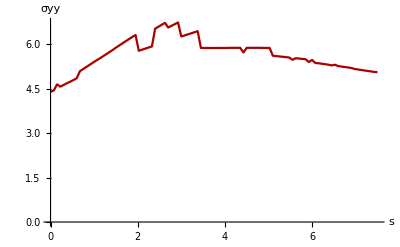

```mathematica
nx=100;
S=L-a;
σy=Table[
{S(i-1)/nx,
SMTPostData["σyy",Point[{S(i-1)/nx+a,H/2}]]},
{i,1,nx+1}];
ListLinePlot[σy,AxesLabel->{"s","σyy"},PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,S},{0,All}}]
```

```mathematica
(*β=Sqrt[Sec[Pi a /L]]*)
β=Sqrt[(4L/(Pi a)) Tan[Pi a /(4 L)]];
(*σinf=σy⟦1,2⟧;*)
σinf=q;
Kfactor=β σinf Sqrt[Pi a];
Kfactor2=σinf*Sqrt[Pi a]*((1-(a/(2L))+0.326*(a/L)^2)/Sqrt[1-(a/L)]);
Print["Fattore di intensificazione degli sforzi teorico 1: ",N[Kfactor]]
Print["Fattore di intensificazione degli sforzi teorico 2: ",N[Kfactor2]]
(*Print["Rapporto: ",N[Kfactor/Sqrt[Pi a]]]*)
```

```mathematica
SMTPostData["v",Point[{0,H/2}]]
```

-0.198929

## Final plate

```mathematica
<<AceFEM`;
```

```mathematica
Npassi=11;
harden=Table[600+i((1600-600)/Npassi),{i,0,Npassi-1}];
σyo=Table[175+i((450-175)/Npassi),{i,0,Npassi-1}];
myv=Table[{0i,0j},{i,1,Length[harden]},{j,1,Length[σyo]}];
Do[Do[
DomainDefinition["Q1EPS","σYO"->σyo⟦j⟧,"H"->harden⟦i⟧];
solveSimulation["animation"->False,"ExportAnimation"->False];
myv⟦i,j⟧=SMTPostData["v",Point[{0,H/2+0.01 H}]];
Print["σyo=",σyo⟦j⟧,", H=",harden⟦i⟧, ", displ= ",myv⟦i,j⟧];
Print[Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]]
,{i,1,Length[harden]}],{j,1,Length[σyo]}]
myv
ListLinePlot[Table[{harden⟦i⟧,myv⟦i,(Length[myv]+1)/2⟧},{i,1,Length[myv]}]]
ListLinePlot[Table[{σyo⟦i⟧,myv⟦(Length[myv]+1)/2,i⟧},{i,1,Length[myv]}]]
list=Flatten[Table[{harden⟦i⟧,σyo⟦j⟧,myv⟦i,j⟧},{i,1,Length[myv]},{j,1,Length[myv]}],1];
ListContourPlot[list,PlotLegends->Automatic]
```

{600,7600/11,8600/11,9600/11,10600/11,11600/11,12600/11,13600/11,14600/11,15600/11,16600/11}

σyo=175, H=600, displ= 2.90884

-Graphics-

σyo=175, H=7600/11, displ= 2.53152

-Graphics-

σyo=175, H=8600/11, displ= 2.24196

-Graphics-

σyo=175, H=9600/11, displ= 2.01273

-Graphics-

σyo=175, H=10600/11, displ= 1.82676

-Graphics-

σyo=175, H=11600/11, displ= 1.67286

-Graphics-

σyo=175, H=12600/11, displ= 1.54339

-Graphics-

σyo=175, H=13600/11, displ= 1.43297

-Graphics-

σyo=175, H=14600/11, displ= 1.33767

-Graphics-

σyo=175, H=15600/11, displ= 1.2546

-Graphics-

σyo=175, H=16600/11, displ= 1.18154

-Graphics-

σyo=200, H=600, displ= 2.4744

-Graphics-

σyo=200, H=7600/11, displ= 2.1537

-Graphics-

σyo=200, H=8600/11, displ= 1.90759

-Graphics-

σyo=200, H=9600/11, displ= 1.71276

-Graphics-

σyo=200, H=10600/11, displ= 1.55469

-Graphics-

σyo=200, H=11600/11, displ= 1.42387

-Graphics-

σyo=200, H=12600/11, displ= 1.31383

-Graphics-

σyo=200, H=13600/11, displ= 1.21997

-Graphics-

σyo=200, H=14600/11, displ= 1.13897

-Graphics-

σyo=200, H=15600/11, displ= 1.06836

-Graphics-

σyo=200, H=16600/11, displ= 1.00626

-Graphics-

σyo=225, H=600, displ= 2.04098

-Graphics-

σyo=225, H=7600/11, displ= 1.77694

-Graphics-

σyo=225, H=8600/11, displ= 1.5743

-Graphics-

σyo=225, H=9600/11, displ= 1.41388

-Graphics-

σyo=225, H=10600/11, displ= 1.28373

-Graphics-

σyo=225, H=11600/11, displ= 1.17602

-Graphics-

σyo=225, H=12600/11, displ= 1.08541

-Graphics-

σyo=225, H=13600/11, displ= 1.00812

-Graphics-

σyo=225, H=14600/11, displ= 0.941431

-Graphics-

σyo=225, H=15600/11, displ= 0.883288

-Graphics-

σyo=225, H=16600/11, displ= 0.832149

-Graphics-

σyo=250, H=600, displ= 1.62543

-Graphics-

σyo=250, H=7600/11, displ= 1.41589

-Graphics-

σyo=250, H=8600/11, displ= 1.25507

-Graphics-

σyo=250, H=9600/11, displ= 1.12776

-Graphics-

σyo=250, H=10600/11, displ= 1.02446

-Graphics-

σyo=250, H=11600/11, displ= 0.938967

-Graphics-

σyo=250, H=12600/11, displ= 0.867046

-Graphics-

σyo=250, H=13600/11, displ= 0.805697

-Graphics-

σyo=250, H=14600/11, displ= 0.752746

-Graphics-

σyo=250, H=15600/11, displ= 0.706581

-Graphics-

σyo=250, H=16600/11, displ= 0.665977

-Graphics-

σyo=275, H=600, displ= 1.2336

-Graphics-

σyo=275, H=7600/11, displ= 1.07538

-Graphics-

σyo=275, H=8600/11, displ= 0.953944

-Graphics-

σyo=275, H=9600/11, displ= 0.857791

-Graphics-

σyo=275, H=10600/11, displ= 0.779773

-Graphics-

σyo=275, H=11600/11, displ= 0.715195

-Graphics-

σyo=275, H=12600/11, displ= 0.66086

-Graphics-

σyo=275, H=13600/11, displ= 0.61451

-Graphics-

σyo=275, H=14600/11, displ= 0.574505

-Graphics-

σyo=275, H=15600/11, displ= 0.539624

-Graphics-

σyo=275, H=16600/11, displ= 0.508942

-Graphics-

σyo=300, H=600, displ= 0.868933

-Graphics-

σyo=300, H=7600/11, displ= 0.758443

-Graphics-

σyo=300, H=8600/11, displ= 0.673628

-Graphics-

σyo=300, H=9600/11, displ= 0.60646

-Graphics-

σyo=300, H=10600/11, displ= 0.551948

-Graphics-

σyo=300, H=11600/11, displ= 0.506815

-Graphics-

σyo=300, H=12600/11, displ= 0.468836

-Graphics-

σyo=300, H=13600/11, displ= 0.436443

-Graphics-

σyo=300, H=14600/11, displ= 0.408489

-Graphics-

σyo=300, H=15600/11, displ= 0.384115

-Graphics-

σyo=300, H=16600/11, displ= 0.362676

-Graphics-

σyo=325, H=600, displ= 0.544882

-Graphics-

σyo=325, H=7600/11, displ= 0.476748

-Graphics-

σyo=325, H=8600/11, displ= 0.424458

-Graphics-

σyo=325, H=9600/11, displ= 0.383065

-Graphics-

σyo=325, H=10600/11, displ= 0.34947

-Graphics-

σyo=325, H=11600/11, displ= 0.321663

-Graphics-

σyo=325, H=12600/11, displ= 0.298269

-Graphics-

σyo=325, H=13600/11, displ= 0.27831

-Graphics-

σyo=325, H=14600/11, displ= 0.261082

-Graphics-

σyo=325, H=15600/11, displ= 0.246066

-Graphics-

σyo=325, H=16600/11, displ= 0.232871

-Graphics-

σyo=350, H=600, displ= 0.278845

-Graphics-

σyo=350, H=7600/11, displ= 0.245663

-Graphics-

σyo=350, H=8600/11, displ= 0.220198

-Graphics-

σyo=350, H=9600/11, displ= 0.200058

-Graphics-

σyo=350, H=10600/11, displ= 0.183717

-Graphics-

σyo=350, H=11600/11, displ= 0.170223

-Graphics-

σyo=350, H=12600/11, displ= 0.158891

-Graphics-

σyo=350, H=13600/11, displ= 0.14924

-Graphics-

σyo=350, H=14600/11, displ= 0.140913

-Graphics-

σyo=350, H=15600/11, displ= 0.133663

-Graphics-

σyo=350, H=16600/11, displ= 0.127301

-Graphics-

σyo=375, H=600, displ= 0.0939033

-Graphics-

σyo=375, H=7600/11, displ= 0.0857319

-Graphics-

σyo=375, H=8600/11, displ= 0.0793877

-Graphics-

σyo=375, H=9600/11, displ= 0.0743135

-Graphics-

σyo=375, H=10600/11, displ= 0.0701525

-Graphics-

σyo=375, H=11600/11, displ= 0.0666736

-Graphics-

σyo=375, H=12600/11, displ= 0.063723

-Graphics-

σyo=375, H=13600/11, displ= 0.0611851

-Graphics-

σyo=375, H=14600/11, displ= 0.0589748

-Graphics-

σyo=375, H=15600/11, displ= 0.0570323

-Graphics-

σyo=375, H=16600/11, displ= 0.0553091

-Graphics-

σyo=400, H=600, displ= 0.0299493

-Graphics-

σyo=400, H=7600/11, displ= 0.0297864

-Graphics-

σyo=400, H=8600/11, displ= 0.0296314

-Graphics-

σyo=400, H=9600/11, displ= 0.0294836

-Graphics-

σyo=400, H=10600/11, displ= 0.0293429

-Graphics-

σyo=400, H=11600/11, displ= 0.0292085

-Graphics-

σyo=400, H=12600/11, displ= 0.0290799

-Graphics-

σyo=400, H=13600/11, displ= 0.0289566

-Graphics-

σyo=400, H=14600/11, displ= 0.028838

-Graphics-

σyo=400, H=15600/11, displ= 0.0287239

-Graphics-

σyo=400, H=16600/11, displ= 0.0286138

-Graphics-

σyo=425, H=600, displ= 0.0233066

-Graphics-

σyo=425, H=7600/11, displ= 0.0232709

-Graphics-

σyo=425, H=8600/11, displ= 0.0232359

-Graphics-

σyo=425, H=9600/11, displ= 0.0232015

-Graphics-

σyo=425, H=10600/11, displ= 0.0231677

-Graphics-

σyo=425, H=11600/11, displ= 0.0231345

-Graphics-

σyo=425, H=12600/11, displ= 0.0231019

-Graphics-

σyo=425, H=13600/11, displ= 0.0230698

-Graphics-

σyo=425, H=14600/11, displ= 0.0230383

-Graphics-

σyo=425, H=15600/11, displ= 0.0230072

-Graphics-

σyo=425, H=16600/11, displ= 0.0229766

-Graphics-

{{2.90884,2.4744,2.04098,1.62543,1.2336,0.868933,0.544882,0.278845,0.0939033,0.0299493,0.0233066},{2.53152,2.1537,1.77694,1.41589,1.07538,0.758443,0.476748,0.245663,0.0857319,0.0297864,0.0232709},{2.24196,1.90759,1.5743,1.25507,0.953944,0.673628,0.424458,0.220198,0.0793877,0.0296314,0.0232359},{2.01273,1.71276,1.41388,1.12776,0.857791,0.60646,0.383065,0.200058,0.0743135,0.0294836,0.0232015},{1.82676,1.55469,1.28373,1.02446,0.779773,0.551948,0.34947,0.183717,0.0701525,0.0293429,0.0231677},{1.67286,1.42387,1.17602,0.938967,0.715195,0.506815,0.321663,0.170223,0.0666736,0.0292085,0.0231345},{1.54339,1.31383,1.08541,0.867046,0.66086,0.468836,0.298269,0.158891,0.063723,0.0290799,0.0231019},{1.43297,1.21997,1.00812,0.805697,0.61451,0.436443,0.27831,0.14924,0.0611851,0.0289566,0.0230698},{1.33767,1.13897,0.941431,0.752746,0.574505,0.408489,0.261082,0.140913,0.0589748,0.028838,0.0230383},{1.2546,1.06836,0.883288,0.706581,0.539624,0.384115,0.246066,0.133663,0.0570323,0.0287239,0.0230072},{1.18154,1.00626,0.832149,0.665977,0.508942,0.362676,0.232871,0.127301,0.0553091,0.0286138,0.0229766}}

-Graphics-

-Graphics-

-Graphics-

```mathematica
DomainDefinition["Q1EPS","σYO"->200,"H"->1000];
solveSimulation["animation"->False,"ExportAnimation"->False];
myv=SMTPostData["v",Point[{0,0.01 H+H/2}]]
myv=SMTPostData["v",Point[{0,H/2}]]
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

1.49951

0.0350827

-Graphics-

Multiplier increment Δλ is not a number.
Description :   Δλ= -1.+λf[0.1]
Version: 7.303 MacOSX (3 Aug 21) (MMA 12.3) Module: SMTNextStep
See also: SMTNextStep  AceFEM Troubleshooting  Continue

$Aborted

```mathematica
myv=SMTPostData["v",Point[{0,H/2}]]
myv=SMTPostData["v",Point[{0,0.01 H+H/2}]]
```

0.00334201

0.532912

```mathematica
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

-Graphics-

```mathematica
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

-Graphics-